```mathematica
GeneralizedFlintHills[cscPower_,jPower_,nMax_]:=Plot[Sum[N[Csc[j]^(cscPower)/j^(jPower)],{j,1,n}],{n,1,nMax}];
```

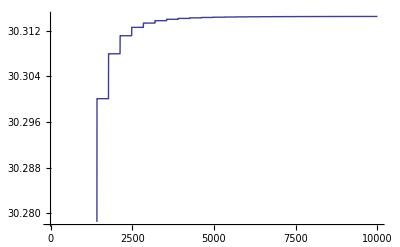

```mathematica
GeneralizedFlintHills[2,3,10000]
(*\Sigma_{i=1}^n \frac{\csc^2 i}{i^3} for n≤10000 *)
```

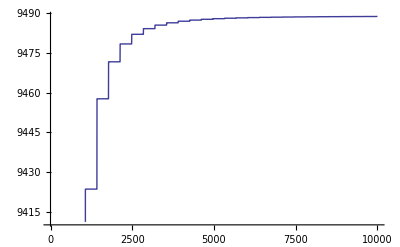

```mathematica
GeneralizedFlintHills[2,2,10000]
(*\Sigma_{i=1}^n \frac{\csc^2 i}{i^2} for n≤10000 *)
```